```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
ctColor=Blue;
```

```mathematica
ccColor=RGBColor["#ff1f5b"];
```

```mathematica
(********************Import V1 axon data****************************)
```

```mathematica
v1DateMouseSessionList={{"082120","Mouse21060","Session2"},{"082320","Mouse21060","Session2"},{"090820","Mouse21067","Session2"},{"092020","Mouse21067","Session2"},{"080221","Mouse21108","Session1"},{"062522","Mouse23007","Session1"},{"062922","Mouse23007","Session1"},{"020421","Mouse23329","Session1"},{"021321","Mouse23329","Session1"},{"030121","Mouse23329","Session1"},{"030621","Mouse23329","Session1"},{"121820","Mouse23365","Session1"},{"122020","Mouse23365","Session1"},{"121020","Mouse23379","Session1"},{"121820","Mouse23379","Session1"},{"101620","Mouse23392","Session2"},{"101820","Mouse23392","Session3"},{"102520","Mouse23392","Session1"},{"101620","Mouse23393","Session1"},{"101520","Mouse23395","Session2"}};
```

```mathematica
v1AxonNums=Length/@Table[ToExpression[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",v1DateMouseSessionList[[n,1]],"/",v1DateMouseSessionList[[n,2]],"/",v1DateMouseSessionList[[n,3]],"/moco/SubROIs/SubROIsList.txt"]]],{n,1,Length[v1DateMouseSessionList]}];
```

```mathematica
subROIsV1axons=Flatten[Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",v1DateMouseSessionList[[n,1]],"/",v1DateMouseSessionList[[n,2]],"/",v1DateMouseSessionList[[n,3]],"/",v1DateMouseSessionList[[n,1]],"_",v1DateMouseSessionList[[n,2]],"_",v1DateMouseSessionList[[n,3]],"_","subROICrossCorrs",".txt"],"List"]),{n,1,Length[v1DateMouseSessionList]}]];
```

```mathematica
roisV1axons=Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",v1DateMouseSessionList[[n,1]],"/",v1DateMouseSessionList[[n,2]],"/",v1DateMouseSessionList[[n,3]],"/",v1DateMouseSessionList[[n,1]],"_",v1DateMouseSessionList[[n,2]],"_",v1DateMouseSessionList[[n,3]],"_","pairwisePartialCrossCorrs",".txt"],"List"]),{n,1,Length[v1DateMouseSessionList]}];
```

```mathematica
(**********************Import LP axon data**************************)
```

```mathematica
lpDateMouseSessionList={{"070122","Mouse23067","Session1"},{"070722","Mouse23067","Session1"},{"063022","Mouse23075","Session1"},{"070822","Mouse23075","Session2"},{"010721","Mouse23339","Session1"},{"011421","Mouse23339","Session2"},{"030921","Mouse23339","Session1"},{"011221","Mouse23369","Session1"},{"011521","Mouse23369","Session1"},{"031121","Mouse23369","Session1"},{"102820","Mouse23377","Session2"},{"102920","Mouse23377","Session2"},{"110120","Mouse23377","Session1"},{"110220","Mouse23377","Session2"},{"120120","Mouse23377","Session2"},{"103120","Mouse23378","Session2"},{"120420","Mouse23378","Session1"},{"120220","Mouse23378","Session2"},{"111520","Mouse23384","Session2"},{"111720","Mouse23384","Session1"},{"120420","Mouse23384","Session1"},{"101920","Mouse23394","Session1"},{"102020","Mouse23394","Session2"},{"100720","Mouse23399","Session2"},{"101020","Mouse23399","Session1"}};
```

```mathematica
lpAxonNums=Length/@Table[ToExpression[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lpDateMouseSessionList[[n,1]],"/",lpDateMouseSessionList[[n,2]],"/",lpDateMouseSessionList[[n,3]],"/moco/SubROIs/SubROIsList.txt"]]],{n,1,Length[lpDateMouseSessionList]}];
```

```mathematica
subROIsLPaxons=Flatten[Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lpDateMouseSessionList[[n,1]],"/",lpDateMouseSessionList[[n,2]],"/",lpDateMouseSessionList[[n,3]],"/",lpDateMouseSessionList[[n,1]],"_",lpDateMouseSessionList[[n,2]],"_",lpDateMouseSessionList[[n,3]],"_","subROICrossCorrs",".txt"],"List"]),{n,1,Length[lpDateMouseSessionList]}]];
```

```mathematica
roisLPaxons=Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lpDateMouseSessionList[[n,1]],"/",lpDateMouseSessionList[[n,2]],"/",lpDateMouseSessionList[[n,3]],"/",lpDateMouseSessionList[[n,1]],"_",lpDateMouseSessionList[[n,2]],"_",lpDateMouseSessionList[[n,3]],"_","pairwisePartialCrossCorrs",".txt"],"List"]),{n,1,Length[lpDateMouseSessionList]}];
```

```mathematica
(**********************Import LM axon data**************************)
```

```mathematica
lmDateMouseSessionList={{"092221","Mouse22422","Session1"},{"100421","Mouse22422","Session1"},{"102021","Mouse22422","Session1"},{"102121","Mouse22436","Session1"},{"081221" ,"Mouse22437","Session2"},{"081521","Mouse22437","Session1"},{"081821","Mouse22437","Session1"},{"082421","Mouse22437","Session2"},{"092321","Mouse22472","Session1"},{"101021","Mouse22472","Session1"},{"102821","Mouse22472","Session2"},{"070822","Mouse22518","Session1"},{"071122","Mouse22518","Session1"},{"070922","Mouse23014","Session1"},{"071422","Mouse23014","Session1"},{"071522","Mouse23025","Session1"},{"072022","Mouse23025","Session1"},{"071222","Mouse23100","Session1"},{"071322","Mouse23100","Session1"}};
```

```mathematica
lmAxonNums=Length/@Table[ToExpression[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lmDateMouseSessionList[[n,1]],"/",lmDateMouseSessionList[[n,2]],"/",lmDateMouseSessionList[[n,3]],"/moco/SubROIs/SubROIsList.txt"]]],{n,1,Length[lmDateMouseSessionList]}];
```

```mathematica
subROIsLMaxons=Flatten[Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lmDateMouseSessionList[[n,1]],"/",lmDateMouseSessionList[[n,2]],"/",lmDateMouseSessionList[[n,3]],"/",lmDateMouseSessionList[[n,1]],"_",lmDateMouseSessionList[[n,2]],"_",lmDateMouseSessionList[[n,3]],"_","subROICrossCorrs",".txt"],"List"]),{n,1,Length[lmDateMouseSessionList]}]];
```

```mathematica
roisLMaxons=Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",lmDateMouseSessionList[[n,1]],"/",lmDateMouseSessionList[[n,2]],"/",lmDateMouseSessionList[[n,3]],"/",lmDateMouseSessionList[[n,1]],"_",lmDateMouseSessionList[[n,2]],"_",lmDateMouseSessionList[[n,3]],"_","pairwisePartialCrossCorrs",".txt"],"List"]),{n,1,Length[lmDateMouseSessionList]}];
```

```mathematica
(**********************Import CT dendrite data**************************)
```

```mathematica
ctDateMouseSessionList={{"041823","Mouse21531","Session1"},{"041923","Mouse21531","Session1"},{"041823","Mouse23138","Session1"},{"041923","Mouse23138","Session1"},{"042023","Mouse23138","Session1"},{"051723","Mouse21532","Session1"},{"051823","Mouse21532","Session1"},{"050523","Mouse23195","Session1"},{"052523","Mouse23195","Session1"}};
```

```mathematica
ctAxonNums=Length/@Table[ToExpression[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ctDateMouseSessionList[[n,1]],"/",ctDateMouseSessionList[[n,2]],"/",ctDateMouseSessionList[[n,3]],"/moco/SubROIs/SubROIsList.txt"]]],{n,1,Length[ctDateMouseSessionList]}];
```

```mathematica
subROIsCTaxons=Flatten[Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ctDateMouseSessionList[[n,1]],"/",ctDateMouseSessionList[[n,2]],"/",ctDateMouseSessionList[[n,3]],"/",ctDateMouseSessionList[[n,1]],"_",ctDateMouseSessionList[[n,2]],"_",ctDateMouseSessionList[[n,3]],"_","subROICrossCorrs",".txt"],"List"]),{n,1,Length[ctDateMouseSessionList]}]];
```

```mathematica
roisCTaxons=Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ctDateMouseSessionList[[n,1]],"/",ctDateMouseSessionList[[n,2]],"/",ctDateMouseSessionList[[n,3]],"/",ctDateMouseSessionList[[n,1]],"_",ctDateMouseSessionList[[n,2]],"_",ctDateMouseSessionList[[n,3]],"_","pairwisePartialCrossCorrs",".txt"],"List"]),{n,1,Length[ctDateMouseSessionList]}];
```

```mathematica
(**********************Import CC dendrite data**************************)
```

```mathematica
ccDateMouseSessionList={{"051623","Mouse23112","Session1"},{"051723","Mouse23112","Session1"},{"052523","Mouse23158","Session1"},{"052923","Mouse23158","Session1"},{"051623","Mouse23166","Session1"},{"051723","Mouse23166","Session1"},{"050123","Mouse23184","Session1"},{"050423","Mouse23184","Session1"}};
```

```mathematica
ccAxonNums=Length/@Table[ToExpression[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ccDateMouseSessionList[[n,1]],"/",ccDateMouseSessionList[[n,2]],"/",ccDateMouseSessionList[[n,3]],"/moco/SubROIs/SubROIsList.txt"]]],{n,1,Length[ccDateMouseSessionList]}];
```

```mathematica
subROIsCCaxons=Flatten[Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ccDateMouseSessionList[[n,1]],"/",ccDateMouseSessionList[[n,2]],"/",ccDateMouseSessionList[[n,3]],"/",ccDateMouseSessionList[[n,1]],"_",ccDateMouseSessionList[[n,2]],"_",ccDateMouseSessionList[[n,3]],"_","subROICrossCorrs",".txt"],"List"]),{n,1,Length[ccDateMouseSessionList]}]];
```

```mathematica
roisCCaxons=Table[Part[#,2]&/@(ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",ccDateMouseSessionList[[n,1]],"/",ccDateMouseSessionList[[n,2]],"/",ccDateMouseSessionList[[n,3]],"/",ccDateMouseSessionList[[n,1]],"_",ccDateMouseSessionList[[n,2]],"_",ccDateMouseSessionList[[n,3]],"_","pairwisePartialCrossCorrs",".txt"],"List"]),{n,1,Length[ccDateMouseSessionList]}];
```

```mathematica
(******************V1 axon ROI and subROI distributions***************************)
```

```mathematica
badData[x_]:=Not[MatchQ[x,_?NumberQ]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{DeleteCases[subROIsV1axons,_?badData],DeleteCases[Flatten@roisV1axons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Blend[{v1Color,Black}],v1Color}),PerformanceGoal->"Speed",PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
h2=Histogram[{DeleteCases[subROIsV1axons,_?badData],DeleteCases[Flatten@roisV1axons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->{{Blend[{v1Color,Black}],v1Color},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
bin=Min[{2*InterquartileRange[DeleteCases[subROIsV1axons,_?badData]]*(Length[DeleteCases[subROIsV1axons,_?badData]]^(-1/3)),2*InterquartileRange[DeleteCases[Flatten@roisV1axons,_?badData]]*(Length[DeleteCases[Flatten@roisV1axons,_?badData]]^(-1/3))}];
```

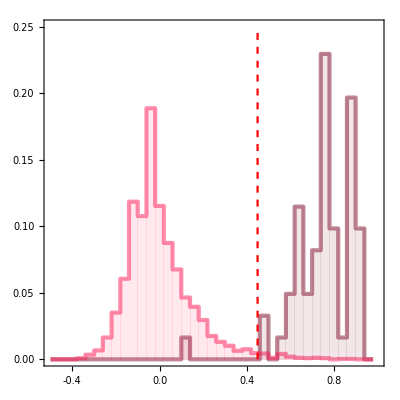

```mathematica
Show[hline,h2,ListLinePlot[{{0.45,0},{0.45,0.25}},PlotStyle->{Red,Dashed}],PlotRange->{{-0.5,1},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

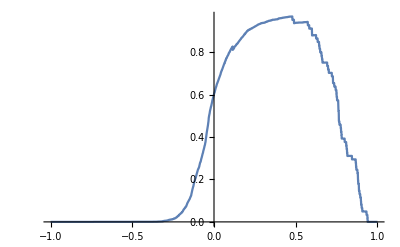

```mathematica
Plot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisV1axons,_?badData],_?badData]],x]-CDF[EmpiricalDistribution[DeleteCases[subROIsV1axons,_?badData]],x],{x,-1,1},PlotRange->All](***Plot difference between CDFs and find maximum, which is the separation threshold***)
```

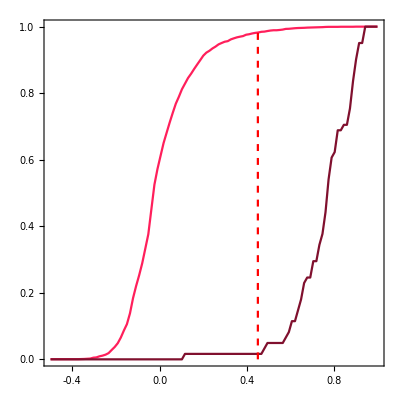

```mathematica
Show[DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisV1axons,_?badData],_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->v1Color],DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[subROIsV1axons,_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->Blend[{v1Color,Black}]],ListLinePlot[{{0.45,0},{0.45,1}},PlotStyle->{Red,Dashed}],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(******************LP axon ROI and subROI distributions***************************)
```

```mathematica
badData[x_]:=Not[MatchQ[x,_?NumberQ]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{DeleteCases[subROIsLPaxons,_?badData],DeleteCases[Flatten@roisLPaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Blend[{lpColor,Black}],lpColor}),PerformanceGoal->"Speed",PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
h2=Histogram[{DeleteCases[subROIsLPaxons,_?badData],DeleteCases[Flatten@roisLPaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->{{Blend[{lpColor,Black}],lpColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
bin=Min[{2*InterquartileRange[DeleteCases[subROIsLPaxons,_?badData]]*(Length[DeleteCases[subROIsLPaxons,_?badData]]^(-1/3)),2*InterquartileRange[DeleteCases[Flatten@roisLPaxons,_?badData]]*(Length[DeleteCases[Flatten@roisLPaxons,_?badData]]^(-1/3))}];
```

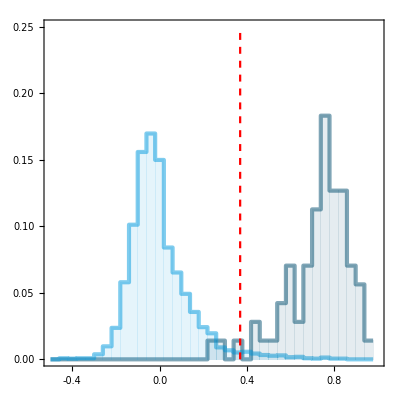

```mathematica
Show[hline,h2,ListLinePlot[{{0.37,0},{0.37,0.25}},PlotStyle->{Red,Dashed}],PlotRange->{{-0.5,1},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

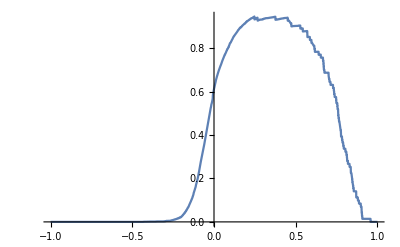

```mathematica
Plot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisLPaxons,_?badData],_?badData]],x]-CDF[EmpiricalDistribution[DeleteCases[subROIsLPaxons,_?badData]],x],{x,-1,1},PlotRange->All](***Plot difference between CDFs and find maximum, which is the separation threshold***)
```

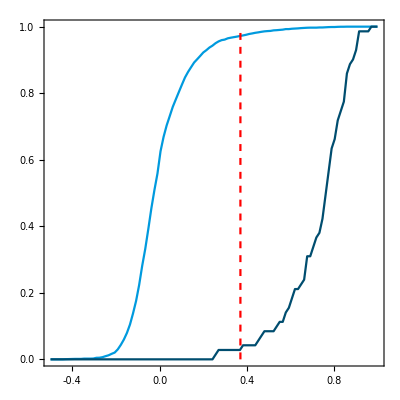

```mathematica
Show[DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisLPaxons,_?badData],_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->lpColor],DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[subROIsLPaxons,_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->Blend[{lpColor,Black}]],ListLinePlot[{{0.37,0},{0.37,1}},PlotStyle->{Red,Dashed}],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(******************LM axon ROI and subROI distributions***************************)
```

```mathematica
badData[x_]:=Not[MatchQ[x,_?NumberQ]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{DeleteCases[subROIsLMaxons,_?badData],DeleteCases[Flatten@roisLMaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Blend[{lmColor,Black}],lmColor}),PerformanceGoal->"Speed",PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
h2=Histogram[{DeleteCases[subROIsLMaxons,_?badData],DeleteCases[Flatten@roisLMaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->{{Blend[{lmColor,Black}],lmColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
bin=Min[{2*InterquartileRange[DeleteCases[subROIsLMaxons,_?badData]]*(Length[DeleteCases[subROIsLMaxons,_?badData]]^(-1/3)),2*InterquartileRange[DeleteCases[Flatten@roisLMaxons,_?badData]]*(Length[DeleteCases[Flatten@roisLMaxons,_?badData]]^(-1/3))}];
```

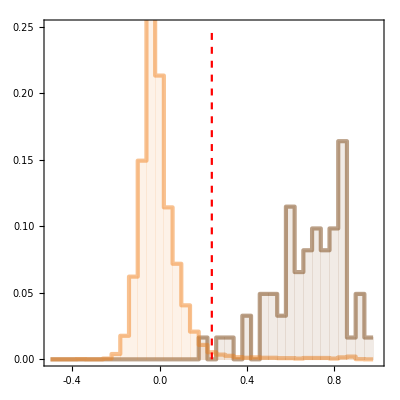

```mathematica
Show[hline,h2,ListLinePlot[{{0.24,0},{0.24,0.25}},PlotStyle->{Red,Dashed}],PlotRange->{{-0.5,1},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

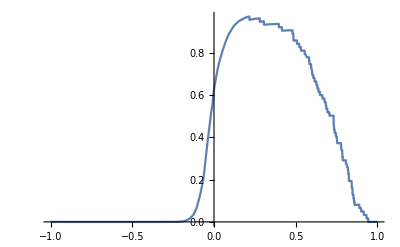

```mathematica
Plot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisLMaxons,_?badData],_?badData]],x]-CDF[EmpiricalDistribution[DeleteCases[subROIsLMaxons,_?badData]],x],{x,-1,1},PlotRange->All](***Plot difference between CDFs and find maximum, which is the separation threshold***)
```

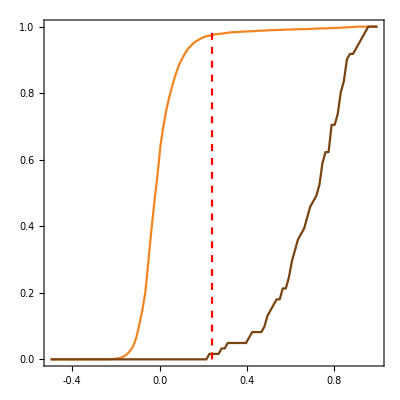

```mathematica
Show[DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisLMaxons,_?badData],_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->lmColor],DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[subROIsLMaxons,_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->Blend[{lmColor,Black}]],ListLinePlot[{{0.24,0},{0.24,1}},PlotStyle->{Red,Dashed}],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(******************CT dendrite ROI and subROI distributions***************************)
```

```mathematica
badData[x_]:=Not[MatchQ[x,_?NumberQ]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{DeleteCases[subROIsCTaxons,_?badData],DeleteCases[Flatten@roisCTaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Blend[{ctColor,Black}],ctColor}),PerformanceGoal->"Speed",PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
h2=Histogram[{DeleteCases[subROIsCTaxons,_?badData],DeleteCases[Flatten@roisCTaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->{{Blend[{ctColor,Black}],ctColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
bin=Min[{2*InterquartileRange[DeleteCases[subROIsCTaxons,_?badData]]*(Length[DeleteCases[subROIsCTaxons,_?badData]]^(-1/3)),2*InterquartileRange[DeleteCases[Flatten@roisCTaxons,_?badData]]*(Length[DeleteCases[Flatten@roisCTaxons,_?badData]]^(-1/3))}];
```

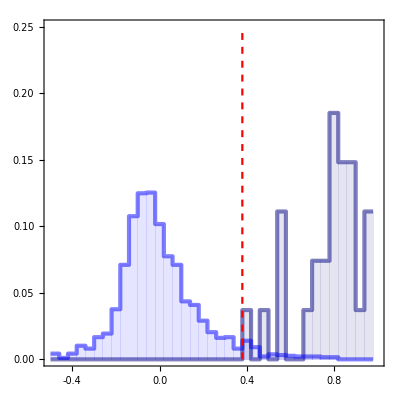

```mathematica
Show[hline,h2,ListLinePlot[{{0.38,0},{0.38,0.25}},PlotStyle->{Red,Dashed}],PlotRange->{{-0.5,1},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

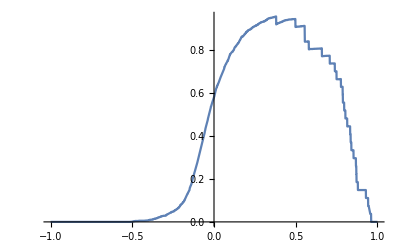

```mathematica
Plot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisCTaxons,_?badData],_?badData]],x]-CDF[EmpiricalDistribution[DeleteCases[subROIsCTaxons,_?badData]],x],{x,-1,1},PlotRange->All](***Plot difference between CDFs and find maximum, which is the separation thresholds***)
```

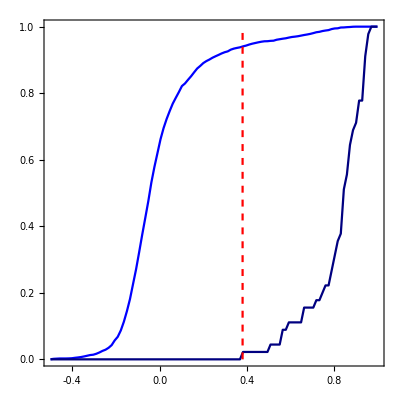

```mathematica
Show[DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisCTaxons,_?badData],_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->ctColor],DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[subROIsCTaxons,_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->Blend[{ctColor,Black}]],ListLinePlot[{{0.38,0},{0.38,1}},PlotStyle->{Red,Dashed}],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

```mathematica
(******************CC dendrite ROI and subROI distributions***************************)
```

```mathematica
badData[x_]:=Not[MatchQ[x,_?NumberQ]]
```

```mathematica
hfn=($MachineEpsilon+#2)/Total[#2]&;
```

```mathematica
h=Histogram[{DeleteCases[subROIsCCaxons,_?badData],DeleteCases[Flatten@roisCCaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->(Directive[#,AbsoluteThickness[3]]&/@{Blend[{ccColor,Black}],ccColor}),PerformanceGoal->"Speed",PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
h2=Histogram[{DeleteCases[subROIsCCaxons,_?badData],DeleteCases[Flatten@roisCCaxons,_?badData]},{-0.5,1,0.04},hfn,ChartStyle->{{Blend[{ccColor,Black}],ccColor},Directive[Opacity[0.1],EdgeForm[]]},PlotRange->{{-0.5,1},{0,0.175}}];
```

```mathematica
hline=h/.rec:{({{_Rectangle}}|{})..}:>Line[Flatten[rec,2]/._[{x_,y_},{X_,Y_},___]:>Sequence[{x,Y},{X,Y}]];
```

```mathematica
bin=Min[{2*InterquartileRange[DeleteCases[subROIsCCaxons,_?badData]]*(Length[DeleteCases[subROIsCCaxons,_?badData]]^(-1/3)),2*InterquartileRange[DeleteCases[Flatten@roisCCaxons,_?badData]]*(Length[DeleteCases[Flatten@roisCCaxons,_?badData]]^(-1/3))}];
```

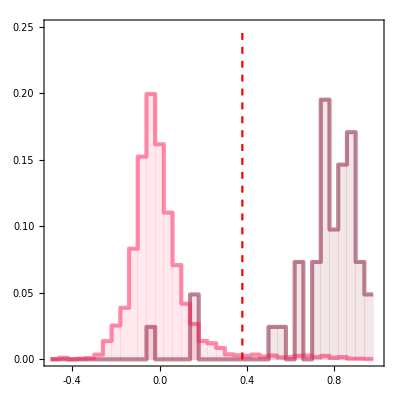

```mathematica
Show[hline,h2,ListLinePlot[{{0.38,0},{0.38,0.25}},PlotStyle->{Red,Dashed}],PlotRange->{{-0.5,1},{0,0.25}},FrameTicks->{{LinTicks[0,0.25,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```

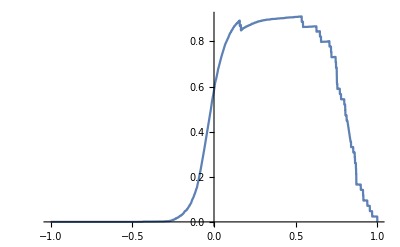

```mathematica
Plot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisCCaxons,_?badData],_?badData]],x]-CDF[EmpiricalDistribution[DeleteCases[subROIsCCaxons,_?badData]],x],{x,-1,1},PlotRange->All](***Plot difference between CDFs and find maximum, which is the separation threshold***)
```

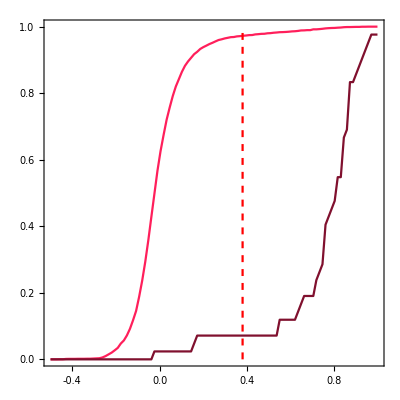

```mathematica
Show[DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[DeleteCases[Flatten@roisCCaxons,_?badData],_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->ccColor],DiscretePlot[CDF[EmpiricalDistribution[DeleteCases[subROIsCCaxons,_?badData]],x],{x,-0.5,1,0.014},Joined->True,FillingStyle->Transparent,PlotStyle->Blend[{ccColor,Black}]],ListLinePlot[{{0.38,0},{0.38,1}},PlotStyle->{Red,Dashed}],FrameTicks->{{LinTicks[0,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-0.5,1,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},AspectRatio->1,FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```